Data:

```mathematica
data=RandomReal[10,{50,2}];
```

NearestFunction:

```mathematica
nf=Nearest[data,DistanceFunction->ChessboardDistance]
```

NearestFunction[…]

Centers:

```mathematica
bincenters=Table[{i,j},{i,1,9,2},{j,1,9,2}]
```

{{{1,1},{1,3},{1,5},{1,7},{1,9}},{{3,1},{3,3},{3,5},{3,7},{3,9}},{{5,1},{5,3},{5,5},{5,7},{5,9}},{{7,1},{7,3},{7,5},{7,7},{7,9}},{{9,1},{9,3},{9,5},{9,7},{9,9}}}

Visualization:

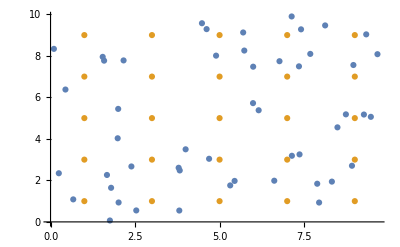

```mathematica
ListPlot[{data,Flatten[bincenters,1]}]
```

```mathematica
nf[bincenters,{Infinity,1}]//MatrixForm
```

({{0.671476,1.0847},{1.79116,1.64325},{1.75603,0.0679311}} | {{1.6689,2.26107},{0.244843,2.34379}} | {{1.98612,4.02846}} | {{0.441031,6.37691},{1.58435,7.76836},{1.5428,7.95085}} | {{0.0992833,8.33619}}
{{2.53576,0.55202},{3.80858,0.547568},{2.01327,0.935232}} | {{2.39176,2.67085},{3.78922,2.60734},{3.82181,2.47845},{3.99554,3.49675}} | {{2.00104,5.44406}} | {{2.16043,7.77943}} | {}
{{5.31452,1.75784},{5.44439,1.97408}} | {{4.68976,3.04094}} | {{5.98919,5.72153}} | {{5.9937,7.477}} | {{4.61611,9.28715},{4.47889,9.5709},{5.69792,9.12559},{5.73101,8.25462},{4.89631,8.00961}}
{{7.8882,1.83863},{7.94383,0.932555},{6.6175,1.98431}} | {{7.13899,3.18513},{7.3651,3.25154}} | {{6.15597,5.37798}} | {{7.34827,7.49406},{6.77207,7.74138}} | {{7.40945,9.27652},{7.13211,9.89717},{7.68286,8.09352}}
{{8.32188,1.94067}} | {{8.91616,2.7053}} | {{8.73623,5.18093},{9.26931,5.17233},{9.47455,5.06163},{8.48673,4.55484}} | {{8.9584,7.55811}} | {{9.33747,9.03423},{8.12264,9.46528},{9.67008,8.0798}})